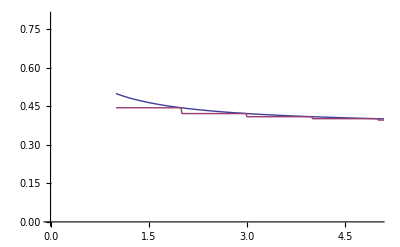

```mathematica
Clear[a,f]
a[n_]:= 1/(1+1/n)^n;
f[x_]:= 1/(1 + 1/x)^x;
lower=Interpolation[Table[{n,a[n]},{n,1,20}],InterpolationOrder->0];
Plot[{f[x],lower[x]},{x,1,50},PlotRange->{{0,5},{0,0.8}}]
```

```mathematica
a[n_]:=1/(1+n);
Limit[a[n],n->Infinity]
```

0

```mathematica
NestList[1/(1+#) &,0,40]
```

{0,1,1/2,2/3,3/5,5/8,8/13,13/21,21/34,34/55,55/89,89/144,144/233,233/377,377/610,610/987,987/1597,1597/2584,2584/4181,4181/6765,6765/10946,10946/17711,17711/28657,28657/46368,46368/75025,75025/121393,121393/196418,196418/317811,317811/514229,514229/832040,832040/1346269,1346269/2178309,2178309/3524578,3524578/5702887,5702887/9227465,9227465/14930352,14930352/24157817,24157817/39088169,39088169/63245986,63245986/102334155,102334155/165580141}

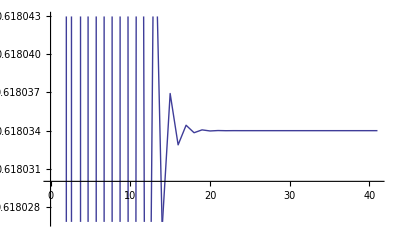

```mathematica
ListLinePlot[NestList[1/(1+ #)&,30,40]]
```

```mathematica
g [x] = (1+ x)/β
NestList[g,(1+β)/α,5]
```

Set::write: Tag Times in 1 + β/x[x] is Protected.

(1+x)/β

{(1+β)/α,(1+β)/x[(1+β)/α],(1+β)/x[(1+β)/x[(1+β)/α]],(1+β)/x[(1+β)/x[(1+β)/x[(1+β)/α]]],(1+β)/x[(1+β)/x[(1+β)/x[(1+β)/x[(1+β)/α]]]],(1+β)/x[(1+β)/x[(1+β)/x[(1+β)/x[(1+β)/x[(1+β)/α]]]]]}

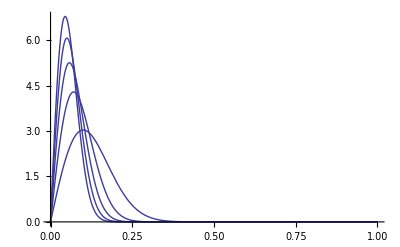

```mathematica
f[x_,n_]:=n*x Exp[-n x^2]
Plot[Table[f[x,50*n],{n,1,5}],{x,0,1},PlotRange->All]
```

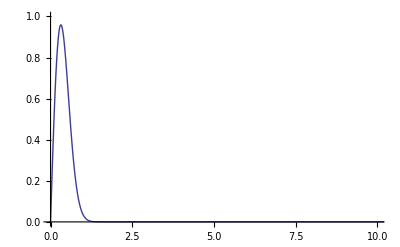

```mathematica
Plot[5*x Exp[-5*x^2],{x,0,20},PlotRange->{{0,10},{0,1}}]
```

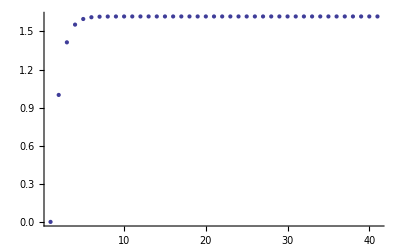

```mathematica
ListPlot[NestList[Sqrt[1+#]&,0,40]]
```

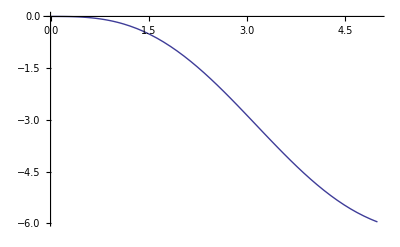

```mathematica
Plot[Sin[x]-x,{x,0,5},PlotRange->All]
```

```mathematica
Plot[x^2]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[x^2]